```mathematica
backgroundsolution[args_]:= Module[
{startI = 0,
endI = 100,
ϕcosmological = 0,
k = 16 Pi^2},
Shooter = args[[2]];
ϕ0 = args[[1]];
backgroundsolutioninterior= NDSolve[{D[u[r,t],r,r] == -k D[u[r,t],t,t],u[r,0] ==Sin[r] √k,u[startI,t] ==  ϕ0},
u,{r,startI,endI},{t,startI,endI}];
Proximity= (u[endI,endI]/.backgroundsolutioninterior) -ϕcosmological;
If[Shooter,Prepend[Proximity,ϕ0],backgroundsolutioninterior]
]
```

```mathematica
start=1000;
end = 10000000;
```

```mathematica
solutions = Parallelize[Table[backgroundsolution[{x,True}],{x,Range[start,end ,(end-start)/1000]}]];
```

```mathematica
solutions
```

{}

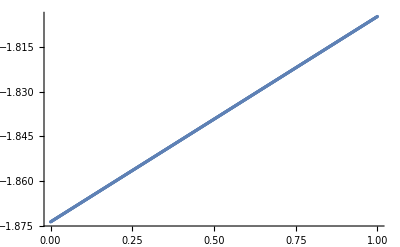

```mathematica
ListPlot[solutions]
```

```mathematica
sol = backgroundsolution[{0,False}]
```

{{u→InterpolatingFunction[{{0., 100.}, {0., 100.}}, <>]}}

```mathematica
Clear[η]
```

```mathematica
η[t_]:=D[u[r,t]/.sol,r]/.r->1
```

```mathematica
u[1,t]/.sol
```

{InterpolatingFunction[{{0., 100.}, {0., 100.}}, <>][1,t]}

```mathematica
η[x_,t_]:= u[x,t]/.sol
```

```mathematica
D[η[r,t],r]/.r->1
```

{InterpolatingFunction[{{0., 100.}, {0., 100.}}, <>][1,t]}

```mathematica
Plot3D[D[η[x,t],x],{x,0,100},{t,0,100},AxesLabel->Automatic]
```

General::ivar: 0.00715 is not a valid variable.

General::ivar: 7.15001 is not a valid variable.

General::ivar: 14.2929 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics3D-

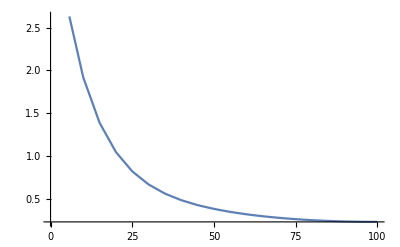

```mathematica
Plot[η[t],{t,0,100}]
```

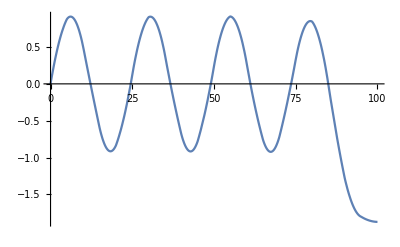

```mathematica
Plot[u[r,100]/.sol,{r,0,100}]
```